```mathematica
eqn = y''[x]-(y[x])^3
DSolve[eqn==0,y'[x],x]
```

-y[x]^3+y''[x]

DSolve[-y[x]^3+y''[x]==0,y'[x],x]

90+90 Tanh[1-(√(√2+2 √2 (-1+x)+√2 (-1+x)^2))/(√2)]

1/Abs[x]

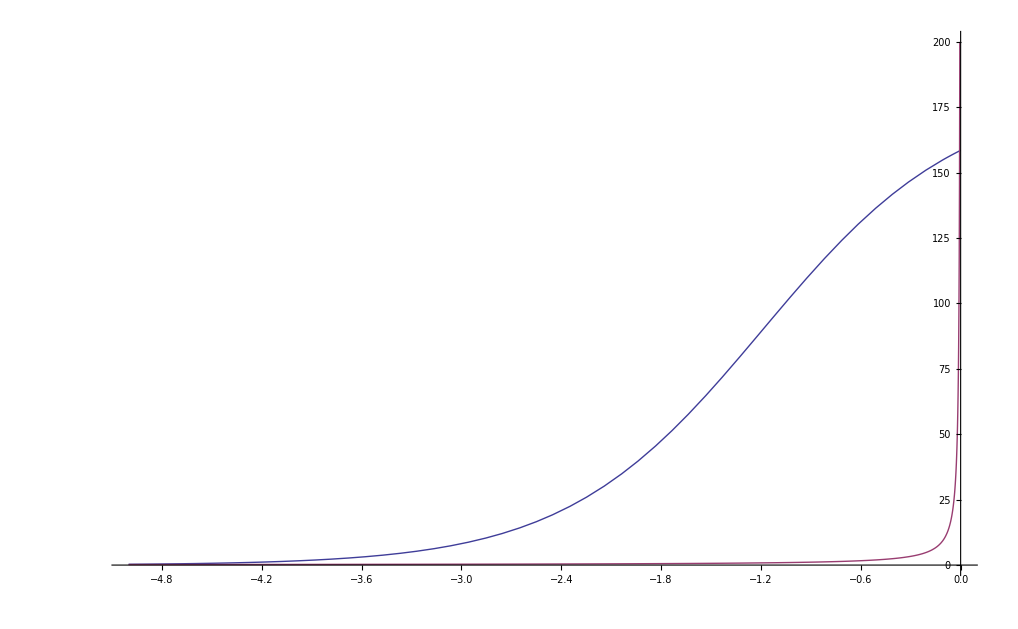

```mathematica
solution = -(90)*JacobiSN[Sqrt[((Sqrt[2])*((x-1)^2))+(2*Sqrt[2]*(x-1))+(Sqrt[2])]/Sqrt[2]-1,1]+90
inflation = Abs[1/x ]
(*adash = D[solution,x]
adoubledash = D[adash,x]
adoubledashcubed = adoubledash^3*)
Plot[{solution,inflation},{x,-5,0}, PlotRange->{0,200}]
```

```mathematica
JacobiSN[x,1/3]
```

```mathematica
Plot[JacobiSN[x,1/3],{x,-10,10}]
```